```mathematica
Needs["PiCbench`"]
```

## 1- Parameter definition

Check the default parameter set

```mathematica
MagnitudeList[]
```

Variable | Value | Description
dx | 1 | Length of cell size in the x dimension
nx | 1024 | Number of cells
qp | 0.0004 | Charge of a macroparticle (absolute value)
mp | 0.0004 | Mass of electron macroparticle
np | 3000 | Number of particles
ionRelMass | 1836.15 | Relative mass of ion species/mass of electrons
dt | 1 | Temporal step
a | 1 | Charge dimenssion in the Maxwell equations
b | 1 | Relative dimension of the magnetic field in the maxwell equations
c | 1 | Speed of light
charSpeed | 0.5 | A characteristic speed of the electrons in the plasma.
charSpeedIons | 0.0116685 | Ion characteristic speed (derived magnitude)
lx | 1024 | System length (derived magnitude)
wp | 0.0342327 | Plasma frecuency (derived magnitude)
debyeLength | 14.6059 | Debye length (derived magnitude)

```mathematica
PrintConditions[]
```

Small cell condition - (dx<<lx) - 1 << 1024

Small time-step condition - (dt<<wp^-1) - 1 << 29.2119

Big world condition - (debyeLength<<lx) - 14.6059 << 1024

Change a certain parameter

```mathematica
PicPar["charSpeed"]=10;
```

```mathematica
PrintConditions[]
```

Small cell condition - (dx<<lx) - 1 << 1024

Small time-step condition - (dt<<wp^-1) - 1 << 29.2119

Big world condition - (debyeLength<<lx) - 292.119 << 1024

```mathematica
PicPar["charSpeed"]=0.5;
```

If intereseted in using different sets in the same notebook/script consider:

```mathematica
CreatePicPar[PicParDemo];
PicParDemo["np"]=10;
```

```mathematica
MagnitudeList[PicParDemo]
PrintConditions[PicParDemo]
```

Variable | Value | Description
dx | 1 | Length of cell size in the x dimension
nx | 1024 | Number of cells
qp | 0.0004 | Charge of a macroparticle (absolute value)
mp | 0.0004 | Mass of electron macroparticle
np | 10 | Number of particles
ionRelMass | 1836.15 | Relative mass of ion species/mass of electrons
dt | 1 | Temporal step
a | 1 | Charge dimenssion in the Maxwell equations
b | 1 | Relative dimension of the magnetic field in the maxwell equations
c | 1 | Speed of light
charSpeed | 0.5 | A characteristic speed of the electrons in the plasma.
charSpeedIons | 0.0116685 | Ion characteristic speed (derived magnitude)
lx | 1024 | System length (derived magnitude)
wp | 0.00197642 | Plasma frecuency (derived magnitude)
debyeLength | 252.982 | Debye length (derived magnitude)

Small cell condition - (dx<<lx) - 1 << 1024

Small time-step condition - (dt<<wp^-1) - 1 << 505.964

Big world condition - (debyeLength<<lx) - 252.982 << 1024

## 2- Initialization

```mathematica
?UniformParticles1D
```

UniformParticles1D[vMax] generates a uniform particle distribution in [0, lx] x [-vMax,vMax].
By default vMax is 2 times the charSpeed parameter.

```mathematica
UniformParticles1D[PicParameters->PicParDemo]
```

{{206.492,-0.323408},{836.083,-0.819234},{612.137,-0.681276},{136.601,0.0509611},{815.988,0.704232},{27.7081,0.346276},{97.151,-0.575842},{37.7366,0.0533807},{955.18,0.388877},{238.739,0.0720659}}

```mathematica
UniformParticles1D[0.01,PicParameters->PicParDemo]
```

{{322.313,-0.00529034},{188.016,-0.00270538},{35.0346,-0.00784433},{114.105,-0.00518335},{997.273,-0.000762894},{690.404,-0.00914173},{674.88,-0.00131028},{227.778,-0.00015436},{906.292,-0.00409022},{231.591,0.00559454}}

```mathematica
electrons=UniformParticles1D[];
```

```mathematica
ions=UniformParticles1D[UseIonDefaults->True];
```

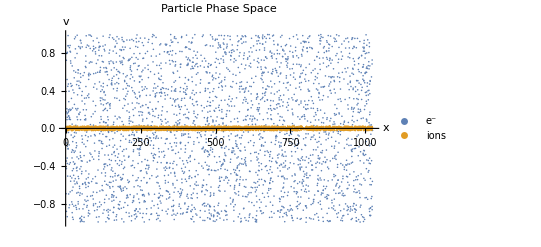

```mathematica
PhaseSpacePlot[{electrons,ions},PlotLegends->{"e^-","ions"}]
```

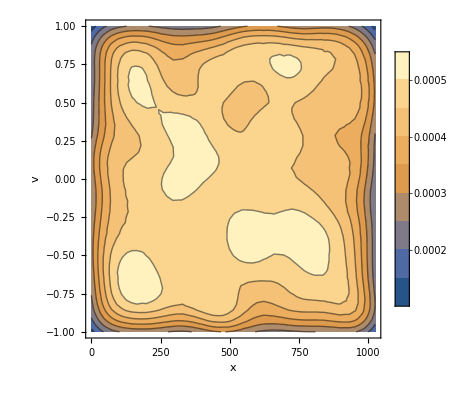

```mathematica
SmoothPhaseSpacePlot[electrons,PlotLegends->Automatic]
```

## 3- Particle to grid

```mathematica
?GetRho1D
```

GetRho1D[] returns a function that calculates rho(particleList).
Relevant parameters are dx,nx,qc.
Can also be used with qc=1 to find number density.

A trick to see the code in a cleaned style:

```mathematica
Begin["PiCbench`Particle2Grid`Private`"];
Quiet[GetRho1D[PicParameters->Symbol,Method->"First-order"],{Table::iterb}]
End[];
```

Function[{particles},Block[{rho,pos,x,i},rho=Table[0.,{1+nx}];For[i=1,i≤Length[particles],i++,x=particles⟦i,1⟧;pos=Floor[x];rho⟦pos+1⟧+=pos+1-x;rho⟦pos+2⟧+=x-pos;];rho⟦1⟧+=rho⟦nx+1⟧;(Drop[rho,-1] qp)/dx]]

Use should be made by using a compiled function

```mathematica
getρ=FCompile[GetRho1D[],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
ρElectron=getρ[electrons];
```

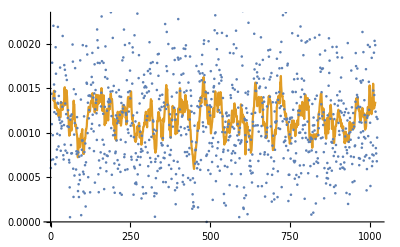

```mathematica
ListPlot[{ρElectron,DebyeMovingAverage[ρElectron]},Joined->{False,True}]
```

```mathematica
ρIon=getρ[ions];
```

## 4- Solving Maxwell

```mathematica
getE=FCompile[GetE1D[],{_Real},{1},{{Re[__],_Real,1}},CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
eField=getE[(ρIon-ρElectron)];
```

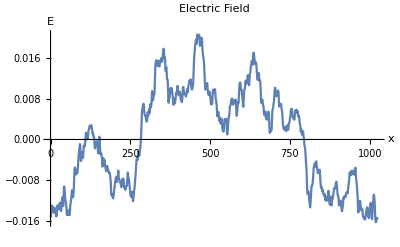

```mathematica
ListPlot[{eField},PlotLabel->"Electric Field",AxesLabel->{"x","E"},Joined->True]
```

## 5- Particle Mover

```mathematica
stepElectrons=FCompile[StepParticles1DES[],{_Real,_Real},{1,2},CompilationTarget->"C",RuntimeOptions->"Speed"];
stepIons=FCompile[StepParticles1DES[UseIonDefaults->True],{_Real,_Real},{1,2},CompilationTarget->"C",RuntimeOptions->"Speed"];
```

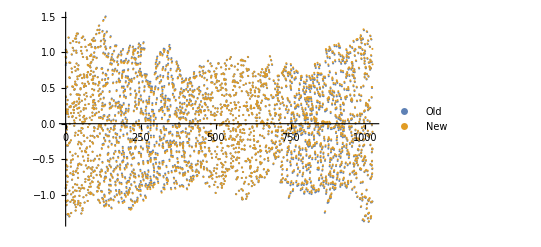

```mathematica
ListPlot[{stepElectrons[eField,electrons],electrons},PlotLegends->{"Old","New"}]
```

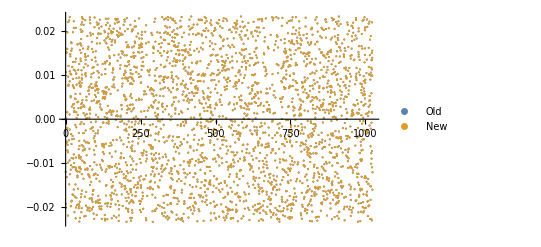

```mathematica
ListPlot[{stepIons[eField,ions],ions},PlotLegends->{"Old","New"}]
```

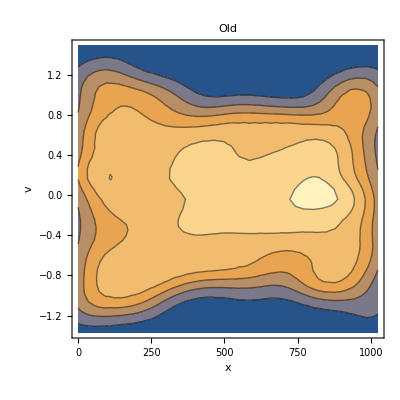
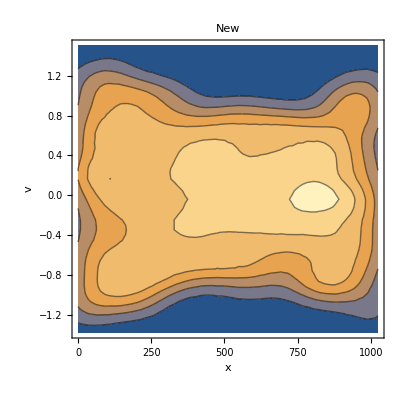

```mathematica
{SmoothPhaseSpacePlot[electrons,PlotLabel->"Old"],SmoothPhaseSpacePlot[stepElectrons[eField,electrons],PlotLabel->"New"]}
```

## 6- A full simulation cycle

```mathematica
electrons=UniformParticles1D[];
ions=UniformParticles1D[UseIonDefaults->True];
nSubsteps=3;(*Steps in time Δt done before saving data for diagnostics*)
nSteps=30;(*Number of cycles repeating the previous*)
```

```mathematica
eFieldList=Table[0,{nSteps}];
ρElectronList=Table[0,{nSteps}];
ρIonList=Table[0,{nSteps}];
electronsList=Table[0,{nSteps}];
ionsList=Table[0,{nSteps}];
AbsoluteTiming[Do[
Do[ (*PiC cycle:*)
(*Particle to grid*)
ρElectron=getρ[electrons];ρIon=getρ[ions];
(*Solve Maxwell*)
eField=getE[(ρIon-ρElectron)];
(*Move particles (includes field interpolation)*)
electrons=stepElectrons[eField,electrons];ions=stepIons[eField,ions];
,{nSubsteps}];
(*Save data*)
eFieldList[[i]]=eField;
ρElectronList[[i]]=ρElectron;
ρIonList[[i]]=ρIon;
electronsList[[i]]=electrons;
ionsList[[i]]=ions;,{i,nSteps}];]
```

{0.080106,Null}

## 7- Diagnostics

```mathematica
Manipulate[ListPlot[{DebyeMovingAverage[ρElectronList[[i]]],DebyeMovingAverage[ρIonList[[i]]]},PlotLabel->"Charge density",AxesLabel->{"x","ρ"},Joined->True,PlotLegends->{"e^-","ions"}],{i,1,Length[ρElectronList],1}]
```

```mathematica
Manipulate[ListPlot[eFieldList[[i]],PlotLabel->"Electric Field",AxesLabel->{"x","E"},PlotRange->{-0.01,0.01}],{i,1,Length[eFieldList],1}]
```

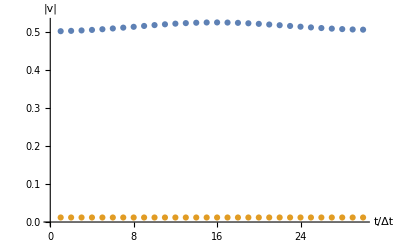

```mathematica
electronsMeanV=Mean[Abs[Last[Transpose[#]]]]&/@electronsList;
ionsMeanV=Mean[Abs[Last[Transpose[#]]]]&/@ionsList;
ListPlot[{electronsMeanV,ionsMeanV},AxesLabel->{"t/Δt","|v|"}]
```

```mathematica
Manipulate[ListPlot[electronsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Electron Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[electronsList],1}]
```

```mathematica
Manipulate[SmoothPhaseSpacePlot[electronsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Electron Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[electronsList],1}]
```

```mathematica
Manipulate[ListPlot[ionsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Ion Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[ionsList],1}]
```

```mathematica
Manipulate[SmoothPhaseSpacePlot[ionsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Ion Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[ionsList],1}]
```